```mathematica
sigma=0.1;
```

```mathematica
mu=0.002;
taua=3;
taub=2;
ra=0.01;
rb=0.01;
epsilonb= 1;
alphaa=0.3;
alphab=0.3;
pt0=1.5;
```

#### MJD

```mathematica
μj=0.01;
σj=0.25;
λ=1;
```

```mathematica
sumgaussPDF[x_,pt_,tau_,mu_,sigma_,μj_,σj_,λ_,kmax_]:=Sum[(λ tau)^k/(k!)Exp[-λ tau] 1/(√(2 π)(√k σj+√tau sigma ))Exp[-1/2((Log[x/pt]-k μj-tau (mu-sigma^2/2))/(√k σj+√tau sigma ))^2]/x,{k,0,kmax}]
```

```mathematica
sumgaussCDF[x_,pt_,tau_,mu_,sigma_,μj_,σj_,λ_,kmax_]:=NIntegrate[sumgaussPDF[t,pt,tau,mu,sigma,μj,σj,λ,kmax],{t,0,x}];
sumgaussCDFERFC[x_,pt_,tau_,mu_,sigma_,μj_,σj_,λ_,kmax_]:=Sum[(λ tau)^k/(k!)Exp[-λ tau]  Erfc[-(Log[x/pt]-k μj-tau (mu-sigma^2/2))/(√2(√k σj+√tau sigma ))]/2,{k,0,kmax}]
```

```mathematica
sumgaussCDFERFC[.1,1,taub,mu,sigma,μj,σj,λ,30]
```

2.027×10^-6

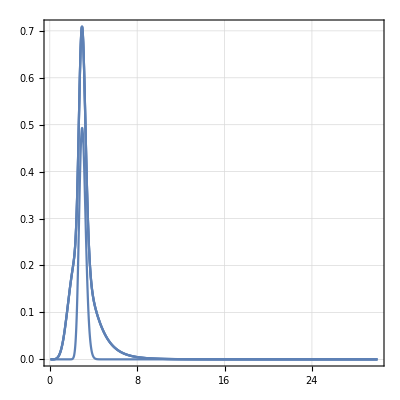

```mathematica
Plot[sumgaussPDF[x,3,taub,mu,sigma,μj,σj,λ,#]&/@{0,10,20,30},{x,0,30},PlotRange->All,AspectRatio->1,Frame->True,GridLines->Automatic]
```

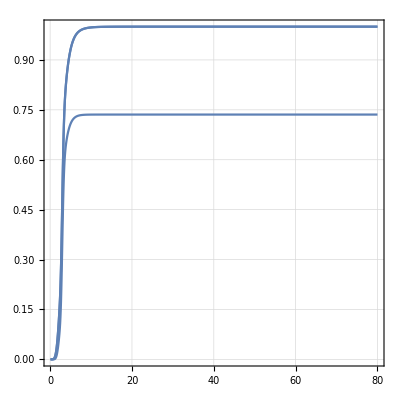

```mathematica
Plot[sumgaussCDFERFC[x,3,taub,mu,sigma,μj,σj,λ,#]&/@{1,10,20},{x,0.1,80},PlotRange->All,AspectRatio->1,Frame->True,GridLines->Automatic]
```

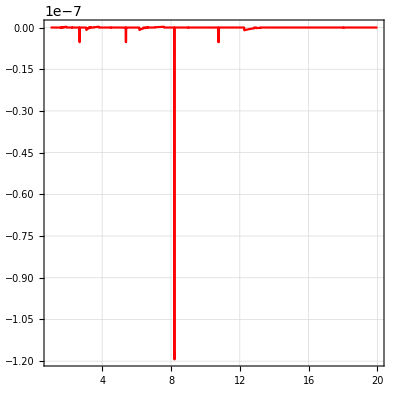

-Graphics-

```mathematica
Show[Plot[1-sumgaussCDF[x,1,taub,mu,sigma,μj,σj,λ,#]/sumgaussCDFERFC[x,1,taub,mu,sigma,μj,σj,λ,#]&/@{10},{x,1,20},PlotRange->All,AspectRatio->1,Frame->True,GridLines->Automatic, PlotStyle->Red]]
```

```mathematica
ϵ[pt_,τ_,μj_,σj_]:=pt Exp[mu τ] Exp[λ τ(Exp[μj+σj^2/2]-1)];
```

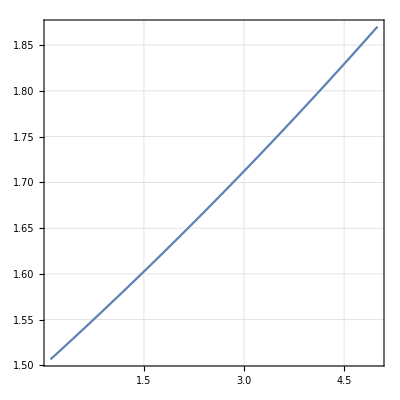

```mathematica
Plot[ϵ[pt0,x,μj,σj],{x,0.1,5},AspectRatio->1,Frame->True,GridLines->Automatic]
```

```mathematica
pt3eq[pstar_,lambda_]:=pstar/Exp[ra(epsilonb+2 taua)]*Exp[ra taub]/(1+alphaa)*1/(Exp[mu taub] Exp[lambda taub(Exp[μj+σj^2/2]-1)]);
```

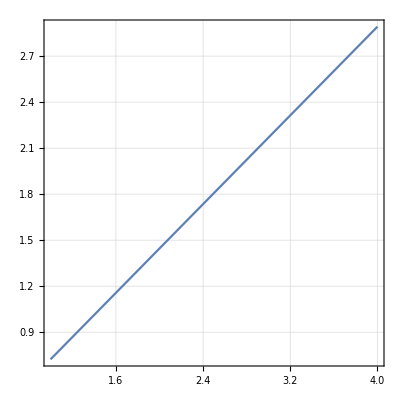
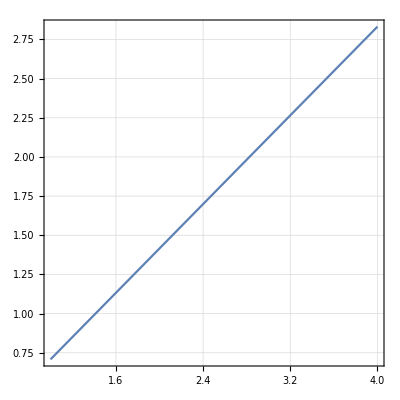
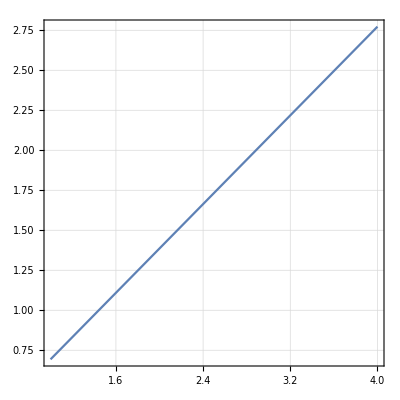
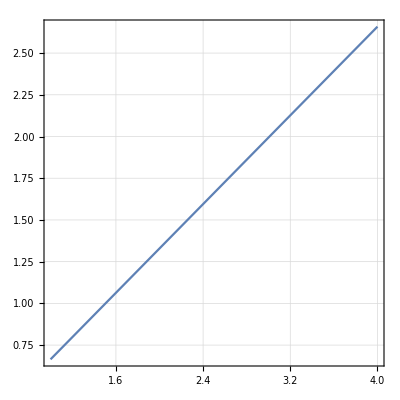
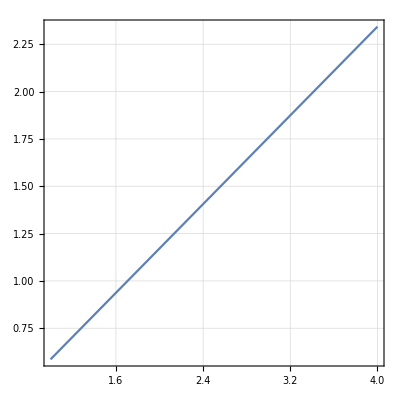

```mathematica
Plot[pt3eq[x,#],{x,1,4},AspectRatio->1,Frame->True,GridLines->Automatic]&/@{0,0.5,1,2,5}
```

```mathematica
ut2bcontMJD[pt2_,pstar_,kmax_]:=((1-sumgaussCDFERFC[pt3eq[pstar,λ]/(1+alphaa),pt2,taub,mu,sigma,μj,σj,λ,kmax])*((1+alphab)*pstar)/Exp[rb*(epsilonb+ra)]+NIntegrate[sumgaussPDF[x,pt2,taub,mu,sigma,μj,σj,λ,kmax]*ϵ[x,2*taub,μj,σj]/Exp[rb*2*taub],{x,0,pt3eq[pstar,λ]}])/Exp[rb*taub]
```

```mathematica
ut2bcontMJD[2,2,#]&/@{1,2,3,4,5,6,7,8,9,10}
```

{2.58119,2.58761,2.58621,2.5851,2.58475,2.58467,2.58465,2.58465,2.58465,2.58465}

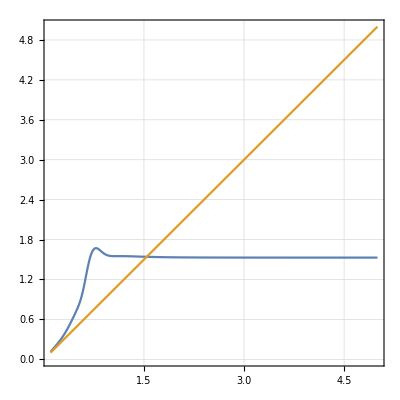
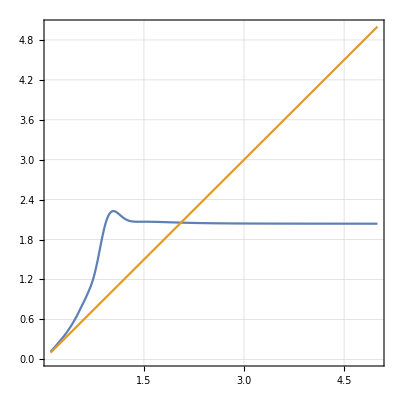
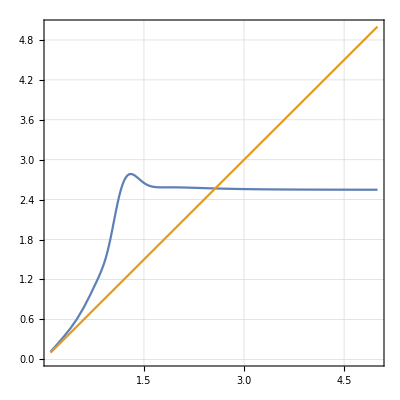
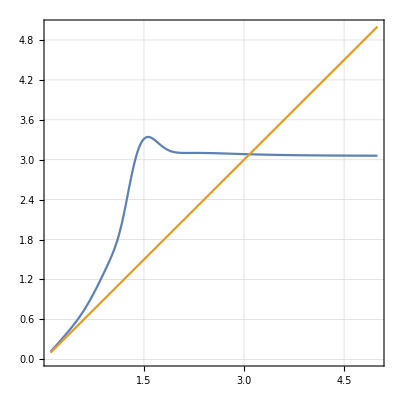

```mathematica
Plot[{ut2bcontMJD[x,#,10],x},{x,0.1,5},AspectRatio->1,Frame->True,GridLines->Automatic]&/@{1.2, 1.6,2.,2.4}
```

```mathematica
lowend[pstar_]:=For[i=0.001,i<5,i+=0.01,If[ut2bcontMJD[i,pstar,10] - i > 0.01, Return[i]]];
highend[pstar_]:=For[i=0.001,i<5,i+=0.01,If[ut2bcontMJD[i,pstar,10] - i > 0.01, For[j=i,j<5,j+=0.01,If[ut2bcontMJD[j,pstar,10] - j < 0.01, Return[j]]]]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1528×10^-8}. NIntegrate obtained 0.00114159 and 9.17006×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.441×10^-8}. NIntegrate obtained 0.00114193 and 0.000450407 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

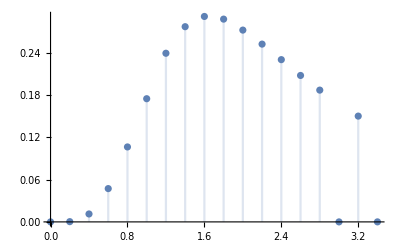

```mathematica
DiscretePlot[successrate[x,lowend[x],highend[x]],{x,0,3.5,0.2},PlotRange->Full]
```

```mathematica
integrand[x_,pt1_,pstar_]:=sumgaussPDF[x,pt1,taua,mu,sigma,μj,σj,λ,10](1-sumgaussCDFERFC[pt3eq[pstar,λ],x,taub,mu,sigma,μj,σj,λ,10]);
successrate[pstar_,pt2min_,pt2max_]:=NIntegrate[integrand[x,pt0,pstar],{x,pt2min,pt2max}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.16149×10^-8}. NIntegrate obtained 0.000746945 and 1.99153×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.44969×10^-8}. NIntegrate obtained 0.000746945 and 2.29264×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.73789×10^-8}. NIntegrate obtained 0.000746945 and 5.29059×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

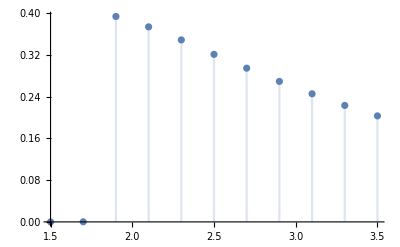

```mathematica
DiscretePlot[successrate[x,0.1,highend[x]],{x,1.5,3.5,0.2},PlotRange->Full]
```